```mathematica
allGraphs6[7174413,"graph"]
```

-Graphics-

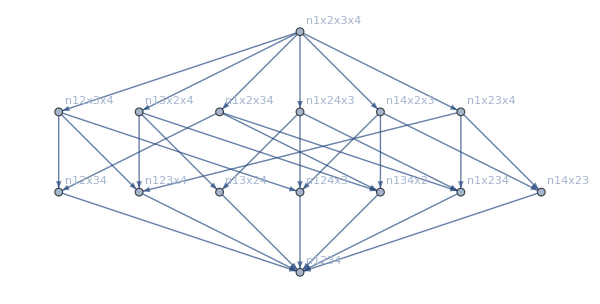
{-Graphics-→-3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5
-Graphics-328-3 x+6 x^2-4 x^3+x^4,-Graphics-→-3 n1x2345+n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
-Graphics-280-3 x+6 x^2-4 x^3+x^4,-Graphics-→-3 n1x2345+n1x234x5+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5
-Graphics-120-3 x+6 x^2-4 x^3+x^4}

```mathematica
With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
allGraphs5[k,"graph"]->
With[{sub2=MobiusGraph4[k,allGraphs4]},
Column[{
allGraphs5[k,"colofourrealnull"],

Labeled[
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->600, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
,
{k,ChromaticPolynomial[allGraphs4[k,"graph"],x]},{Top,Bottom}
]
}
]
]
,{k,Take[Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},EdgeCount[g]>3&&ChromaticPolynomial[g,2]>0]&],3]}]
]
```

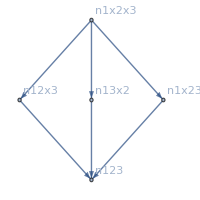
{-Graphics-→n1x2x3x4x5
-Graphics-0x^3,-Graphics-→-n1x2x3x45+n1x2x3x4x5
-Graphics-1-x^2+x^3,-Graphics-→n1x2x3x45
-Graphics-2x^2,-Graphics-→-n1x2x35x4+n1x2x3x4x5
-Graphics-3-x^2+x^3,-Graphics-→n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5
-Graphics-4x-2 x^2+x^3,-Graphics-→n1x2x35x4
-Graphics-6x^2,-Graphics-→-n1x2x34x5+n1x2x3x4x5
-Graphics-9-x^2+x^3,-Graphics-→n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
-Graphics-10x-2 x^2+x^3,-Graphics-→n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5
-Graphics-12x-2 x^2+x^3,-Graphics-→2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5
-Graphics-132 x-3 x^2+x^3,-Graphics-→-n1x2x345+n1x2x3x45
-Graphics-14-x+x^2,-Graphics-→-n1x2x345+n1x2x35x4
-Graphics-16-x+x^2,-Graphics-→n1x2x34x5
-Graphics-18x^2,-Graphics-→-n1x2x345+n1x2x34x5
-Graphics-22-x+x^2,-Graphics-→n1x2x345
-Graphics-26x}

```mathematica
With[{full=MobiusGraph4[13,allGraphs3]},
Table[
allGraphs3[k,"graph"]->
With[{sub2=MobiusGraph4[k,allGraphs3]},
Column[{
allGraphs5[k,"colofourrealnull"],

Labeled[
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->200, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
,
{k,ChromaticPolynomial[allGraphs3[k,"graph"],x]},{Top,Bottom}
]
}
]
]
,{k,Sort[Keys[allGraphs3]]}]
]
```

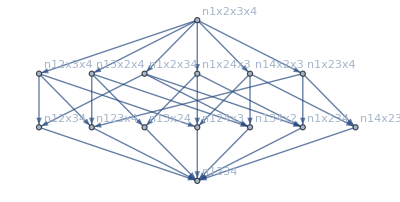
-Graphics-→-Graphics-13
-Graphics-→-Graphics-40
-Graphics-→-Graphics-94
-Graphics-→-Graphics-109
-Graphics-→-Graphics-112
-Graphics-→-Graphics-118
-Graphics-→-Graphics-121
-Graphics-→-Graphics-256
-Graphics-→-Graphics-273
-Graphics-→-Graphics-274
-Graphics-→-Graphics-282
-Graphics-→-Graphics-283
-Graphics-→-Graphics-333
-Graphics-→-Graphics-334
-Graphics-→-Graphics-336
-Graphics-→-Graphics-337
-Graphics-→-Graphics-352
-Graphics-→-Graphics-354
-Graphics-→-Graphics-355
-Graphics-→-Graphics-360
-Graphics-→-Graphics-361
-Graphics-→-Graphics-363
-Graphics-→-Graphics-364
-Graphics-→-Graphics-365
-Graphics-→-Graphics-367
-Graphics-→-Graphics-373
-Graphics-→-Graphics-391
-Graphics-→-Graphics-445
-Graphics-→-Graphics-607

```mathematica
TableForm[
With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
allGraphs4[k,"graph"]->
Labeled[
With[{sub2=MobiusGraph4[k,allGraphs4]},
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->400, VertexLabels->"Name"]
],
{k},{Top}
]
,{k,Select[Sort[Keys[allGraphs4]],ChromaticPolynomial[allGraphs4[#,"graph"],2]==0&]}]
]
]
```

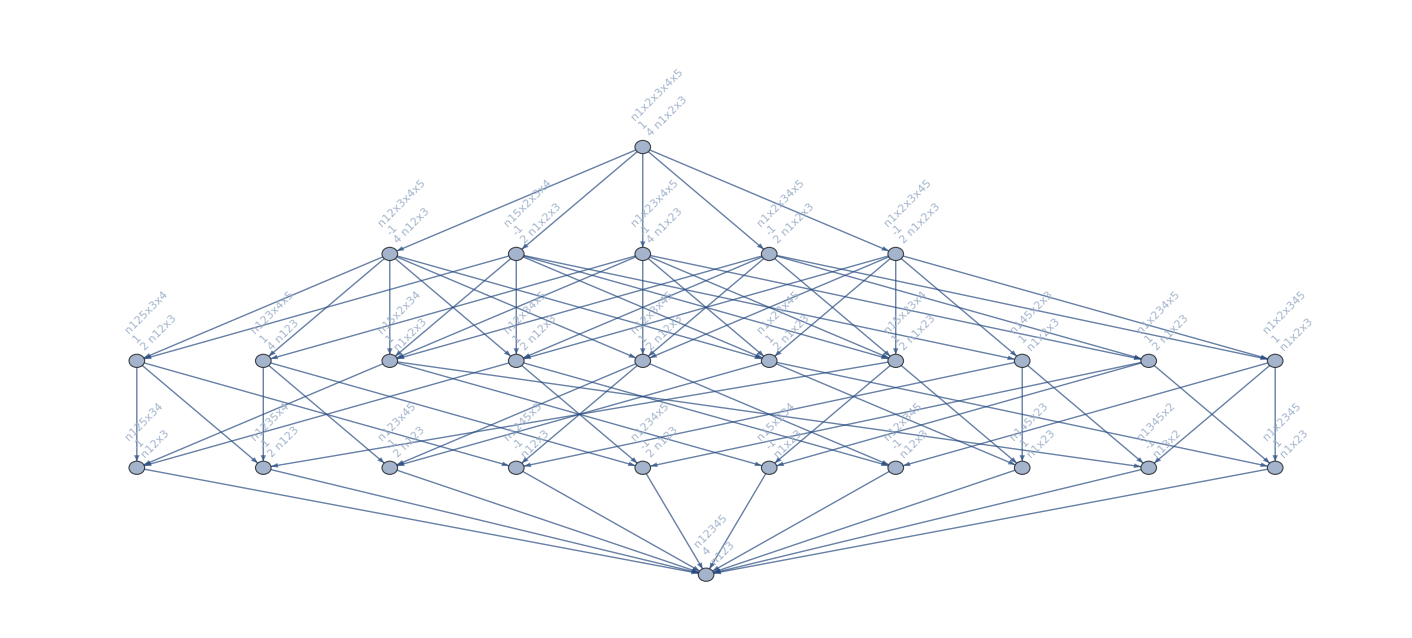

```mathematica
MobiusGraph4[lambdaKey,allGraphs5]
```

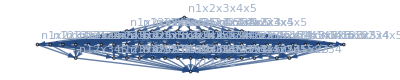
{-Graphics-→-Graphics-20665,-Graphics-→-Graphics-36166}

```mathematica
With[{full=MobiusGraph4[k5Key,allGraphs5]},
Table[
allGraphs5[k,"graph"]->
Labeled[
With[{sub2=MobiusGraph4[k,allGraphs5]},
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->400, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
],
{k},{Top}
]
,{k,{lambdaKey,alfa1Key}}]
]
```